# TranscendentalRange

Generate ranges of transcendental numbers

## Definition

### Auxiliary functions

#### FormulaComplexity

```mathematica
ClearAll[formulaComplexity]

digitSum[int_Integer]:=If[$VersionNumber>=14,DigitSum[int],Total@IntegerDigits[int]]

formulaComplexity[form_?NumericQ]:=
	N@Total[Cases[
			Inactivate[form]
		/.const_?(Quiet@MemberQ[Attributes[#],Constant]&):>1
			/.c_Complex:>ReIm[c]
				/.r:Rational[i1_Integer,i2_Integer]:>{i1,i2}
					/.Inactive[Sqrt][arg_]:>Inactive[Sqrt[{arg,arg}]]
						/.Alternatives[
							Inactive[Power][b_,Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}],
							Inactive[Power][{b_},Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}]]:>
								Table[b,Abs[n]+Abs[m]],
			_Integer,{0,Infinity}]/. j_Integer?NonPositive:>-j+1
				/.i_Integer:>Mean[1/2{5IntegerLength[i],digitSum[i],Total[Last/@FactorInteger[i]],Sqrt[Abs[N[i]]]}]]
```

#### Restricted range

```mathematica
complexitySelect[list_List,c_]:=
	Select[list,formulaComplexity[#]<=c&]

ClearAll[stepSelect]
stepSelect[list_List,d_]:=
	Block[{sel,eln,i},
	eln=list[[1]];
	sel=CreateDataStructure["DynamicArray"];
	sel["Append",eln];
	
	For[i=2,i<=Length[list],i++,
		
		If[Abs[list[[i]]-eln]>=d,

			eln=list[[i]];
			sel["Append",eln],
			
			Continue[]]];
	
	Normal@sel]~Quiet~N::meprec

stepSelect[{},d_]:=
	{}

stepSelect[{},d_,t_:0]:=
	{}
```

```mathematica
restrictRange[main_,compl_,d_:0]:=
	If[d!=0,stepSelect[#,d],#]&[complexitySelect[main,compl]]
```

### Generator ranges

#### AlgebraicRange

```mathematica
ClearAll[algebraicRange]
algebraicRange[args__]:=ResourceFunction["AlgebraicRange"][args];
```

#### FareyRange

```mathematica
ClearAll[fareyRange]
fareyRange[r1_,r2_,r3_]:=
	If[r3>=1,
		ResourceFunction["FareyRange"][r1,r2,r3],
		Which[(*intuitive alternative reciprocal step*)
			MatchQ[r3,Rational[1,_]],
				ResourceFunction["FareyRange"][r1,r2,1/r3],
			MatchQ[r3,Rational[-1,_]],
				Reverse[ResourceFunction["FareyRange"][r2,r1,-1/r3]],
			True,
				failureFareyStep[r3]]]
```

#### Basic range

```mathematica
range[x_,y_,z_,opt_String]:=
Switch[opt,
		"Rational",
			Range[x,y,z],
		"Algebraic",
			algebraicRange[x,y,z],
		"RationalFarey",
			fareyRange[x,y,z],
		"AlgebraicFarey",
			algebraicRange[x,y,z,"FareyRange"->True]]
```

#### Argument failures

```mathematica
failureNotAlgebraics=
Failure["ArgsNotAlgebraic",<|"MessageTemplate"->"The range arguments provided `ls` are not all algebraic numbers.","MessageParameters"-><|"ls"->#|>|>]&;
```

```mathematica
failureFareyStep=Failure["FareyStep",<|"MessageTemplate"->"The step parameter `s` is not allowed with the Farey range option.","MessageParameters"-><|"s"->#|>|>]&;
```

### Methods generalities

#### Transcendental types

All possible methods include the following transcendental functions types:

```mathematica
$trig={Sin,Cos,Tan,Cot,Sec,Csc};
$hyp={Sinh,Cosh,Tanh,Coth,Sech,Csch};
$invtrig={ArcSin,ArcCos,ArcTan,ArcCot,ArcSec,ArcCsc};
$invhyp={ArcSinh,ArcCosh,ArcTanh,ArcCoth,ArcSech,ArcCsch};
$trsctypes=Join[{Exp,Log,Power},$trig,$hyp,$invtrig,$invhyp];
```

#### Domains

Domains for the transcendental functions (namely, for the second arguments of Outer or monotonicOuter):

```mathematica
ClearAll[domain]
domain[_]=True&; 
domain[Log]=#>0&;
domain[Power]=#>0&;
domain[Coth]=#!=0&;
domain[Csch]=#!=0&;
domain[ArcCosh]=#>=1&;
domain[ArcTanh]=-1<#<1&;
domain[ArcCoth]=Abs[#]>1&;
domain[ArcSech]=0<#<=1&;
domain[ArcCsch]=#!=0&;
domain[Tan]=Abs@FractionalPart[#/π]!=1/2&;
domain[Sec]=Abs@FractionalPart[#/π]!=1/2&;
domain[Cot]=FractionalPart[#/π]!=0&;
domain[Csc]=FractionalPart[#/π]!=0&;
domain[ArcSin]=Abs[#]<=1&;
domain[ArcCos]=Abs[#]<=1&;
domain[ArcCot]=#!=0&;
domain[ArcSec]=Abs[#]>=1&;
domain[ArcCsc]=Abs[#]>=1&;
```

#### General testing method

The following general method is simpler to implement but also "naive" in the sense that it uses the default inefficient version of Outer. Then it can be used as a method for testing the more sophisticated efficient implementation with monotonicOuter.

(It is also currently the default method for direct trigonometric functions.)

```mathematica
(*elementary testing range with only one function at a time*)

ClearAll[elemNaiveRange]

elemNaiveRange[x_,y_,z_:1,fun:_Symbol|_String:Exp,opt_String:"Rational"]/;NumericQ[z]:=
Block[
{rgmain,min=If[x<y,x,y],max=If[x<y,y,x]},

(*arguments basic range, to be restricted below*)
rgmain=range[x,y,z,opt];

DeleteCases[
Select[

Outer[

(*function with two arguments*)
Which[
MemberQ[{Exp,Log,Splice@Join[$trig,$hyp,$invtrig,$invhyp]},fun],
	#1fun[#2],
fun===Power,
	#2^#1,
True,
	$Failed]&,

(*first argument*)
Which[
	MemberQ[{Exp,Log,Splice@Join[$trig,$hyp,$invtrig,$invhyp]},fun],
		rgmain,
	fun===Power,
			DeleteCases[rgmain,_Rationals]],

(*second argument*)
Which[
		
		MemberQ[{Log,Power,Coth,Csch,ArcCosh,ArcTanh,ArcCoth,ArcSech,ArcCsch,Tan,Sec,Cot,Csc,ArcSin,ArcCos,ArcCot,ArcSec,ArcCsc},fun],
			Select[rgmain,domain[fun]],

		True,
			rgmain
		]]//Flatten,
min<=#<=max&],
_?(Element[#,Algebraics]&)]]
```

```mathematica
ClearAll[combinedNaiveRange];

Options[combinedNaiveRange]={WorkingPrecision->MachinePrecision,"GeneratorsDomain"->Rationals};

combinedNaiveRange[x_,y_,z_:1,funs_List,opts:OptionsPattern[combinedNaiveRange]]/;NumericQ[z]:=
	Block[{funL,patf,extrarg,prec=OptionValue[WorkingPrecision],optalg=optGenerators[OptionValue["GeneratorsDomain"]]},
		funL=If[funs=!={All},
			Flatten@funs,
			$trsctypes];

		patf=_?(MemberQ[$trsctypes,#]&);
		extrarg=#/.Times[a_, patf[arg_]]|patf[arg_]:>Abs@N[arg,prec]&;

		
Values@Map[First@SortBy[#,extrarg]&,GroupBy[Join@@Map[elemNaiveRange[x,y,z,#,optalg]&,funL],N[#,prec]&]]]
```

```mathematica
sortNaiveRange[x_,y_,z_:1,fun:_Symbol|_String|_List|All,opts:OptionsPattern[combinedNaiveRange]]/;NumericQ[z]:=
	If[z>0,SortBy,ReverseSortBy][combinedNaiveRange[x,y,z,{fun},opts],N[#,OptionValue[WorkingPrecision]]&]
```

#### Monotonic outer

```mathematica
monotonicOuter[fun_Function,{min_,max_},ls1_List,ls2_List,{mi_,mj_},sign_]:=
	Block[{i,j,new,begin,end,rgQ,outer},
		
		outer=CreateDataStructure["DynamicArray"];				

		For[
			Switch[mi,
					1,i=1,
					-1,i=Length[ls1]],
			Switch[mi,
					1,i<=Length[ls1],
					-1,i>=1],
			Switch[mi,
					1,i++,
					-1,i--],

			begin=True;

			end=False;

			For[

				Switch[mj,
					1,j=1,
					-1,j=Length[ls2]],
				Switch[mj,
					1,j<=Length[ls2],
					-1,j>=1],
				Switch[mj,
					1,j++,
					-1,j--],

				

				new=fun[ls1[[i]],ls2[[j]]];
				
				rgQ=min<=new<=max;
				
				If[rgQ,
					begin=False];

				Which[new>max&&sign===1,
						end=True,
					new<min&&sign===-1,
						end=True];
				
				Which[
					rgQ&&!begin,
						outer["Append",new],
					begin&&!end,
						(*this should be avoided with better splitting*)
						Echo[{"redundant",ls1[[i]],ls2[[j]]}];
						Continue[],
					True,
						Break[]]]];

		Normal@outer]//QuietEcho
```

#### Range preprocessing

```mathematica
(*splitRange:split a sorted list into segments at given points*)
ClearAll[splitRange]
splitRange[list_List,splitPts_List,z_,segs_,count_]:=Block[{pts,bounds,n,seg},pts=Sort[splitPts];
bounds=Join[{-Infinity},pts,{Infinity}];
n=Length[bounds]-1;
count=n;
Do[seg=Select[list,bounds[[k]]<=#<=bounds[[k+1]]&];
segs[k]=If[z>0,seg,Reverse[seg]],{k,n}];]
```

```mathematica
(*preprRange:prepare coefficient and argument ranges for monotonicOuter.
#1 (coefficient) takes values in the whole range[x,y,z].
#2 (argument to f) takes values only where f is defined.
Each range is split independently at its own critical points for efficient Break[] in monotonicOuter.*)
ClearAll[preprRange]

preprRange[
{x_,y_,z_,opt_},
{cAlg_,cSing_,cSplit_},
{aDom_,aAlg_,aSing_,aSplit_},
{rc_,ra_,cs_,as_,ncs_,nas_}]:=

Block[{base},

base=range[x,y,z,opt];

(*Coefficient range:full range minus algebraic/singular points*)
rc=base;
If[cAlg=!=None,rc=DeleteCases[rc,cAlg]];
If[Length[cSing]>0,rc=DeleteCases[rc,Alternatives@@cSing]];

(*Argument range:domain-restricted,minus algebraic/singular*)
ra=Select[base,aDom];
If[aAlg=!=None,ra=DeleteCases[ra,aAlg]];
If[Length[aSing]>0,ra=DeleteCases[ra,Alternatives@@aSing]];

splitRange[rc,cSplit,z,cs,ncs];
splitRange[ra,aSplit,z,as,nas];]
```

### Methods implementations

#### Exp

Plot

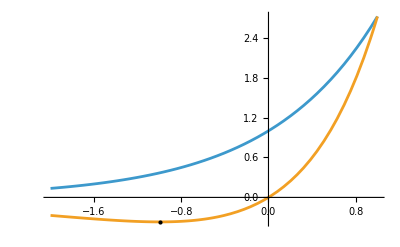

```mathematica
If[$Notebooks,
Plot[{Exp[x],x Exp[x]},{x,-2,1},Epilog->{PointSize@Large,Point@{-1,-Exp[-1]}}]]
```

Definition

```mathematica
coreRange[{f:Exp,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{-1}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},1],monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},-1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Log

Plot

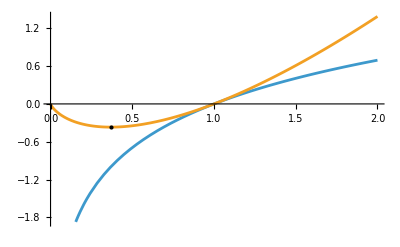

```mathematica
If[$Notebooks,
Plot[{Log[x],x Log[x]},{x,0,2},Epilog->{PointSize@Large,Point@{1/E,-1/E}}]]
```

Definition

```mathematica
coreRange[{f:Log,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],1,{},{1/E,1}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[3],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1],monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},-1],monotonicOuter[fun,{min,max},cs[1],as[3],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Sinh

Plot

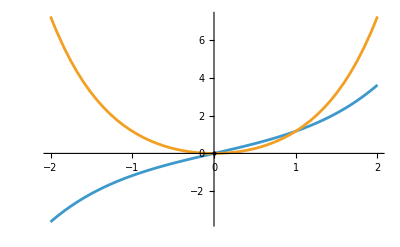

```mathematica
If[$Notebooks,
Plot[{Sinh[x],x Sinh[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:Sinh,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Cosh

Plot

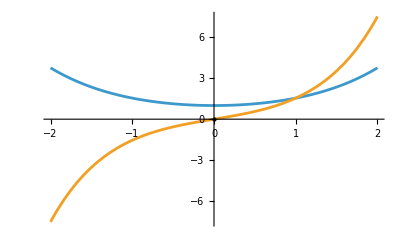

```mathematica
If[$Notebooks,
Plot[{Cosh[x],x Cosh[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:Cosh,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1],
monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1],monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Tanh

Plot

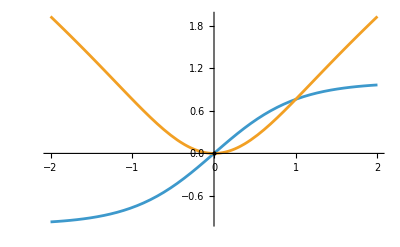

```mathematica
If[$Notebooks,
Plot[{Tanh[x],x Tanh[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:Tanh,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1],monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Coth

Plot

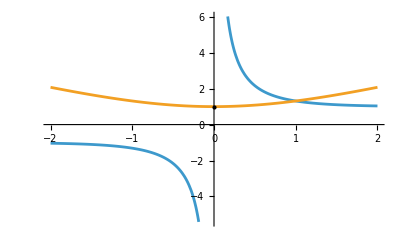

```mathematica
If[$Notebooks,
Plot[{Coth[x],x Coth[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,1}}]]
```

Definition

```mathematica
coreRange[{f:Coth,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{0},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[2],{1,-1},1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},-1],monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Sech

Turning point

```mathematica
turning[Sech,2]=Entity["MathematicalConstant","CothFixedPointConstant"][EntityProperty["MathematicalConstant","NumericalApproximation"]];
```

Plot

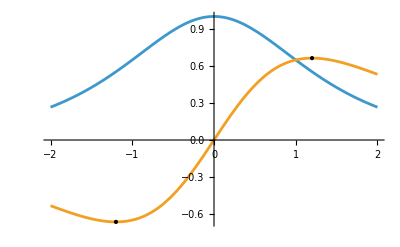

```mathematica
If[$Notebooks,
With[{turn=turning[Sech,2]},
Plot[{Sech[x],x Sech[x]},{x,-2,2},Epilog->{{{PointSize@Large,Point@{-turn,-turn Sech[turn]},{PointSize@Large,Point@{turn,turn Sech[turn]}}}}}]]]
```

Definition

```mathematica
coreRange[{f:Sech,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn,turn=turning[f,2]},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{-turn,0,turn}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[4],{1,1},1],
monotonicOuter[fun,{min,max},cs[2],as[3],{1,1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[4],{-1,1},-1],
monotonicOuter[fun,{min,max},cs[1],as[3],{-1,1},-1],
monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},-1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Csch

Plot

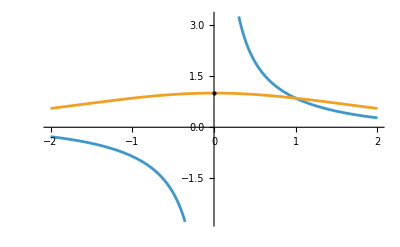

```mathematica
If[$Notebooks,
Plot[{Csch[x],x Csch[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,1}}]]
```

Definition

```mathematica
coreRange[{f:Csch,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{0},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[2],{1,-1},1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},-1],monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcSinh

Plot

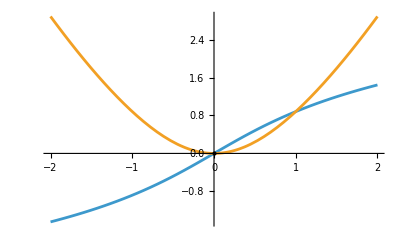

```mathematica
If[$Notebooks,
Plot[{ArcSinh[x],x ArcSinh[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:ArcSinh,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcCosh

Plot

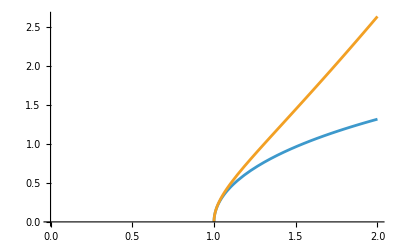

```mathematica
If[$Notebooks,
Plot[{ArcCosh[x],x ArcCosh[x]},{x,0,2},Epilog->{PointSize@Large,Point@{1/E,-1/E}}]]
```

Definition

```mathematica
coreRange[{f:ArcCosh,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],1,{},{}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[
monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},-1]];

Which[0<=x<=y||0<=y<=x,outp,x<=y<=0||y<=x<=0,outn,x<=0&&y>=0,outn~Join~outp,y<=0&&x>=0,outp~Join~outn]]
```

#### ArcTanh

Plot

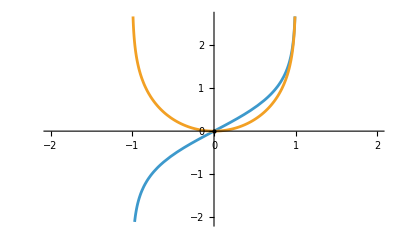

```mathematica
If[$Notebooks,
Plot[{ArcTanh[x],x ArcTanh[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:ArcTanh,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcCoth

Plot

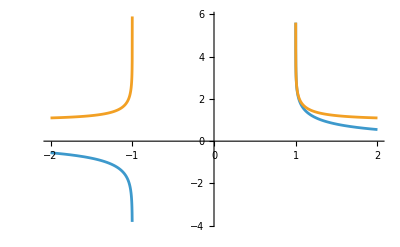

```mathematica
If[$Notebooks,
Plot[{ArcCoth[x],x ArcCoth[x]},{x,-2,2}]]
```

Definition

```mathematica
coreRange[{f:ArcCoth,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{-1,1},{-1,1}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[3],{1,-1},1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[3],{-1,-1},-1],monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcSech

Turning point

```mathematica
rooteq[ArcSech,2]=D[x ArcSech[x],x]==0//PowerExpand//Simplify;
turning[ArcSech,2]=With[{prec=1000},FindRoot[rooteq[ArcSech,2],{x,0.5},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];
```

Plot

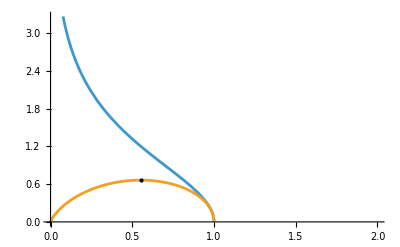

```mathematica
If[$Notebooks,
With[{turn=turning[ArcSech,2]},Plot[{ArcSech[x],x ArcSech[x]},{x,0,2},Epilog->{PointSize@Large,Point@{turn,turn ArcSech[turn]}}]]]
```

Definition

```mathematica
coreRange[{f:ArcSech,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn,turn=turning[f,2]},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],1,{0},{turn}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[
monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,-1},1]];

outn:=Join[
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},-1],
monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},-1]];

Which[0<=x<=y||0<=y<=x,outp,x<=y<=0||y<=x<=0,outn,x<=0&&y>=0,outn~Join~outp,y<=0&&x>=0,outp~Join~outn]]
```

#### ArcCsch

Plot

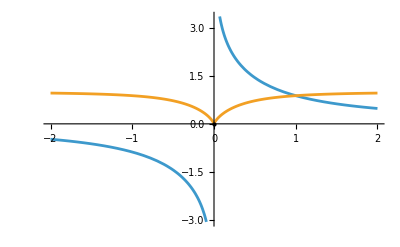

```mathematica
If[$Notebooks,
Plot[{ArcCsch[x],x ArcCsch[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:ArcCsch,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{0},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[2],{1,-1},1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},-1],monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcSin

Plot

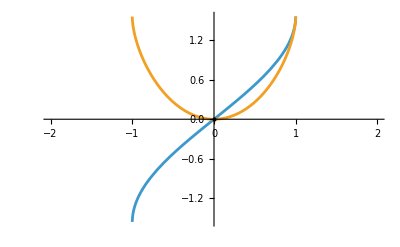

```mathematica
If[$Notebooks,
Plot[{ArcSin[x],x ArcSin[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:ArcSin,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcCos

Turning point

```mathematica
rooteq[ArcCos,2]=D[x ArcCos[x],x]==0//PowerExpand//Simplify;
turning[ArcCos,2]=With[{prec=1000},FindRoot[rooteq[ArcCos,2],{x,0.5},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];
```

Plot

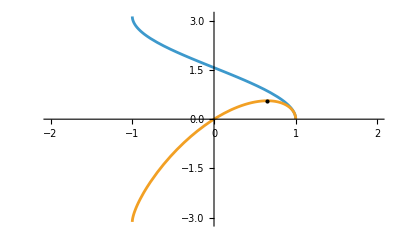

```mathematica
If[$Notebooks,
With[{turn=turning[ArcCos,2]},Plot[{ArcCos[x],x ArcCos[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{turn,turn ArcCos[turn]}}]]]
```

Definition

```mathematica
coreRange[{f:ArcCos,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn,turn=turning[f,2]},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],1,{},{turn}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[
monotonicOuter[fun,{min,max},cs[2],as[2],{1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},1]];

outn:=Join[
monotonicOuter[fun,{min,max},cs[1],as[2],{-1,-1},-1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},-1]];

Which[0<=x<=y||0<=y<=x,outp,x<=y<=0||y<=x<=0,outn,x<=0&&y>=0,outn~Join~outp,y<=0&&x>=0,outp~Join~outn]]
```

#### ArcTan

Plot

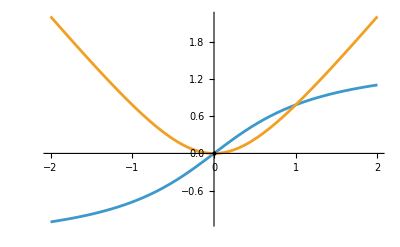

```mathematica
If[$Notebooks,
Plot[{ArcTan[x],x ArcTan[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f:ArcTan,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{0}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[1],as[1],{-1,-1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[2],as[1],{1,-1},-1],monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcCot

Plot

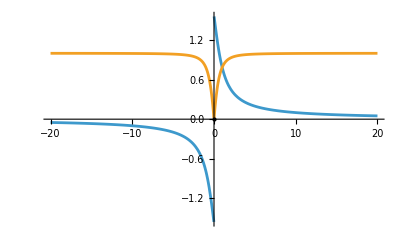

```mathematica
If[$Notebooks,
Plot[{ArcCot[x],x ArcCot[x]},{x,-20,20},Epilog->{PointSize@Large,Point@{0,0}}]]
```

Definition

```mathematica
coreRange[{f : ArcCot, 2}, x_, y_, z_ : 1, opt_String : "Rational"] := 
Block[{fun = # f[#2] &, min = If[z > 0, x, y], max = If[z > 0, y, x], rc, ra, cs, as, ncs, nas, outp, outn},
  
  preprRange[
   {x, y, z, opt},
   {0, {}, {0}},
   {domain[f], 0, {0}, {0}},
   {rc, ra, cs, as, ncs, nas}];
  
  outp := Join[monotonicOuter[fun, {min, max}, cs[2], as[2], {1, -1}, 1],
    monotonicOuter[fun, {min, max}, cs[1], as[1], {-1, 1}, 1]];
  
  outn := Join[monotonicOuter[fun, {min, max}, cs[1], as[2], {-1, -1}, -1], 
  monotonicOuter[fun, {min, max}, cs[2], as[1], {1, 1}, -1]];
  
  Which[
   0 <= x <= y || 0 <= y <= x, outp,
   x <= y <= 0 || y <= x <= 0, outn,
   x <= 0 && y >= 0, outn~Join~outp,
   y <= 0 && x >= 0, outp~Join~outn]]
```

#### ArcSec

Turning point

```mathematica
rooteq[ArcSec,2]=D[ x ArcSec[x],x]==0//PowerExpand//Simplify;
turning[ArcSec,2]=With[{prec=1000},FindRoot[rooteq[ArcSec,2],{x,-10},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];
```

Plot

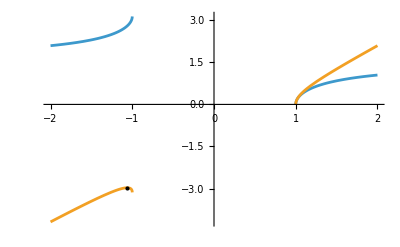

```mathematica
If[$Notebooks,
With[{turn=turning[ArcSec,2]},
Plot[{ArcSec[x],x ArcSec[x]},{x,-2,2},Epilog->{PointSize@Large,Point@{turn,turn ArcSec[turn]}}]]]
```

Definition

```mathematica
coreRange[{f:ArcSec,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn,
turn=turning[f,2]},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],1,{},{turn,-1,1}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[4],{1,1},1],
monotonicOuter[fun,{min,max},cs[2],as[2],{1,1},1],
monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[4],{-1,1},-1],
monotonicOuter[fun,{min,max},cs[1],as[2],{-1,1},-1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### ArcCsc

Plot

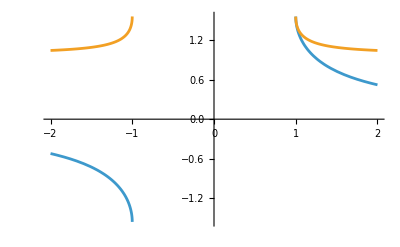

```mathematica
If[$Notebooks,
Plot[{ArcCsc[x],x ArcCsc[x]},{x,-2,2}]]
```

Definition

```mathematica
coreRange[{f:ArcCsc,2},x_,y_,z_:1,opt_String:"Rational"]:=Block[{fun=# f[#2]&,min=If[z>0,x,y],max=If[z>0,y,x],rc,ra,cs,as,ncs,nas,outp,outn},

preprRange[
{x,y,z,opt},
{0,{},{0}},
{domain[f],0,{},{-1,1}},
{rc,ra,cs,as,ncs,nas}];

outp:=Join[monotonicOuter[fun,{min,max},cs[2],as[3],{1,-1},1],
monotonicOuter[fun,{min,max},cs[1],as[1],{-1,1},1]];

outn:=Join[monotonicOuter[fun,{min,max},cs[1],as[3],{-1,-1},-1],monotonicOuter[fun,{min,max},cs[2],as[1],{1,1},-1]];

Which[
0<=x<=y||0<=y<=x,outp,
x<=y<=0||y<=x<=0,outn,
x<=0&&y>=0,outn~Join~outp,
y<=0&&x>=0,outp~Join~outn]]
```

#### Power

Turning point

```mathematica
rooteq[Power,2]=D[ (-x)^x,x]==0//Simplify;
turning[Power,2]=With[{prec=1000},FindRoot[rooteq[Power,2],{x,-0.1},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];
```

Plot

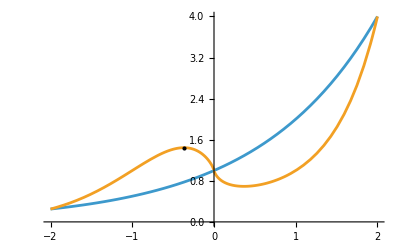

```mathematica
If[$Notebooks,
With[{turn = turning[Power, 2]}, Plot[{Power[2,x], Power[Abs[x],x]}, {x, -2, 2}, Epilog -> {PointSize@Large, Point@{turn,  Power[Abs[turn],turn]}}]]]
```

Definition

```mathematica
coreRange[{f : Power, 2}, x_, y_, z_ : 1, opt_String : "Rational"] := Block[{fun = #1^#2 &, min = If[z > 0, x, y], max = If[z > 0, y, x], rc, ra, cs, as, ncs, nas, outp, outn,
turn=turning[Power,2]},
  
  preprRange[
   {x, y, z, opt},
   {0, {}, {turn,0}},
   {domain[f], 1, {}, {1}},
   {rc, ra, cs, as, ncs, nas}];
 

cs[1]=Select[cs[1],!Element[#,Rationals]&];
cs[2]=Select[cs[2],!Element[#,Rationals]&];
cs[3]=Select[cs[3],!Element[#,Rationals]&];

outp := 
Select[Join[monotonicOuter[fun, {min, max},as[1], cs[3],  {1, 1}, 1],
monotonicOuter[fun, {min, max},as[2], cs[3],  {1, 1}, 1],
monotonicOuter[fun, {min, max},  as[1],cs[2], {1,-1}, 1],
monotonicOuter[fun, {min, max},as[2], cs[2],  {1,- 1}, 1],
monotonicOuter[fun, {min, max},  as[1],cs[1], {1,- 1}, 1],
monotonicOuter[fun, {min, max},as[2], cs[1],  {1, -1}, 1]
    ],True&];
  
  outn := 
{};
  
  Which[
   0 <= x <= y || 0 <= y <= x, outp,
   x <= y <= 0 || y <= x <= 0, outn,
   x <= 0 && y >= 0, outn~Join~outp,
   y <= 0 && x >= 0, outp~Join~outn]]
```

### Main definition

#### Options

```mathematica
ClearAll[TranscendentalRange]

Options[TranscendentalRange]={Method->Exp,"GeneratorsDomain"->Rationals,"FareyRange"->False,"FormulaComplexity"->Infinity,WorkingPrecision->MachinePrecision,"Test"->False(*developer only option*)};
```

```mathematica
ClearAll[optGenerators]
optGenerators[opts:OptionsPattern[TranscendentalRange]]:=
	Block[{plain},
		plain=Switch[OptionValue["GeneratorsDomain"],
						Rationals|{Rationals,Reals},
							"Rational",
						Algebraics|{Algebraics,Reals},
							"Algebraic"];
		If[!OptionValue["FareyRange"],
				plain,
				plain<>"Farey"]]
optGenerators[str_String]:=str
```

#### Combined range

```mathematica
ClearAll[combineMethod]
combineMethod[funL_List,x_,y_,z_,d_,opts:OptionsPattern[TranscendentalRange]]:=
	With[{prec=OptionValue[WorkingPrecision]},SortBy[DeleteDuplicatesBy[Join@@Map[TranscendentalRange[x,y,z,d,Method->#,opts]&,funL],
N[#,prec]&],N[#,prec]&]]
```

#### Semifinal range

```mathematica
ClearAll[transcendentalRange]

Options[transcendentalRange]=Options[TranscendentalRange];

transcendentalRange[{f_,i_},x_,y_,z_:1,opts:OptionsPattern[transcendentalRange]]:=

Block[{prec=OptionValue[WorkingPrecision],rg,rpl,sby,ddby},
		
		(*raw redundant range*)
		rg=coreRange[{f,i},x,y,z,optGenerators[opts]];
	
		(*delete duplicates by N + choose the one with minimal argument*)
		rpl=Switch[i,
					1,f[arg_]:>Abs@N[arg,prec],
					2,Times[a_, f[arg_]]|f[arg_]:>Abs@N[arg,prec]];
		ddby=Values@Map[
			First@MinimalBy[#,#/.rpl&,1]&,	
			
			GroupBy[rg,N[#,prec]&]];

		(*(rev)sort by N*)
		sby=If[z>0,SortBy,ReverseSortBy];
		sby[ddby,N[#,prec]&]]
```

#### Final range

```mathematica
Clear[TranscendentalRange]

TranscendentalRange[x_,opts:OptionsPattern[TranscendentalRange]]:=
	Block[{optcompl,optalg,fullrange,restrcompl},

		If[!Element[{x},Algebraics],
			Return@failureNotAlgebraics[{x}]];

		optcompl=OptionValue["FormulaComplexity"];
		optalg=optGenerators[opts];

		fullrange=Which[

	MemberQ[Join[{Exp,Log,Power},$hyp,$invhyp,$invtrig],OptionValue[Method]]&&!OptionValue["Test"],
			transcendentalRange[{OptionValue[Method],2},1,x,1,opts],

	MemberQ[$trig,OptionValue[Method]]&&!OptionValue["Test"],
			sortNaiveRange[1,x,1,OptionValue[Method],
				"GeneratorsDomain"->optalg,WorkingPrecision->OptionValue[WorkingPrecision]],

	ListQ[OptionValue[Method]],
			combineMethod[OptionValue[Method],1,x,1,0,opts],
						
	OptionValue[Method]===All,
			combineMethod[$trsctypes,1,x,1,0,opts],
						
	MemberQ[$trsctypes,OptionValue[Method]]||OptionValue["Test"],
			sortNaiveRange[1,x,1,OptionValue[Method],
				"GeneratorsDomain"->optalg,WorkingPrecision->OptionValue[WorkingPrecision]],
						
	True,
			$Failed];

		restrcompl=If[optcompl<Infinity,
			complexitySelect[fullrange,optcompl],
			fullrange]]


TranscendentalRange[x_,y_,z_:1,d_:0,opts:OptionsPattern[TranscendentalRange]]/;NumericQ[d]&&NumericQ[z]:=
	Block[{optcompl,optalg,fullrange,restrcompl,restrstep},

		If[!Element[{x,y,z},Algebraics],
			Return@failureNotAlgebraics[{x,y,z}]];

		optcompl=OptionValue["FormulaComplexity"];
		optalg=optGenerators[opts];

		fullrange=Which[

	MemberQ[Join[{Exp,Log,Power},$hyp,$invhyp,$invtrig],OptionValue[Method]]&&!OptionValue["Test"],
			transcendentalRange[{OptionValue[Method],2},x,y,z,opts],
						
	MemberQ[$trig,OptionValue[Method]]&&!OptionValue["Test"],
			sortNaiveRange[x,y,z,OptionValue[Method],"GeneratorsDomain"->optalg],
						
	ListQ[OptionValue[Method]],
			combineMethod[OptionValue[Method],x,y,z,d,opts],
						
	OptionValue[Method]===All,
			combineMethod[$trsctypes,x,y,z,d,opts],
						
	MemberQ[$trsctypes,OptionValue[Method]]||OptionValue["Test"],
			sortNaiveRange[x,y,z,OptionValue[Method],
				"GeneratorsDomain"->optalg,WorkingPrecision->OptionValue[WorkingPrecision]],
						
	True,
			$Failed];

		restrcompl=If[optcompl<Infinity,
			complexitySelect[fullrange,optcompl],
			fullrange];

		restrstep=If[d>0,
			stepSelect[restrcompl,d],
			restrcompl]]
```

## Documentation

### Usage

TranscendentalRange[x]

gives all transcendental numbers of the forms t=b ⅇ^a with 1<=t<=x and a,b algebraics in Range[x].

TranscendentalRange[x,y]

gives all transcendental numbers of the forms t=b ⅇ^a, with x<=t<=y and a,b algebraics in Range[x,y].

TranscendentalRange[x,y,s]

gives all transcendental numbers of the forms t=b ⅇ^a, with x<=t<=y, s>0 and a,b algebraics in Range[x,y,s].

TranscendentalRange[x,y,s,d]

require a lower bound on the steps d.

### Details & Options

TranscendentalRange can systematically generate various types of transcendental numbers.

Transcendental numbers are irrational numbers for which it has been mathematically proven that they cannot be expressed as solutions of any polynomial equation with integer coefficients (that is, they are not Root objects at the exact level).

As for the basic function Range, the first two arguments of TranscendentalRange are the numeric bounds x, y of the range. In other words, all the range elements satisfy x<=t_i<=y.

By default, the range elements are generated according to the Lindemann-Weierstrass theorem, that is linear combinations of exponentials t_i= b ⅇ^a, for all algebraic arguments and coefficients a, b that are members of Range[x,y], or possibly Range[x,y,s] using also a step parameter s as third argument.

This transcendental range definition appears rather natural mathematically, but requires careful implementation as a customized version of Outer, so to avoid producing unnecessary expressions which will be eventually discarded since beyond the bounds.

As it happens for resource function "AlgebraicRange", also the definition of TranscendentalRange allows the user to specify a fourth argument d, to require a minimum absolute value difference between successive transcendentals and thus avoid the tendency to produce very irregular distributions of numeric values.

TranscendentalRange has been designed especially in view of its application to the resource function  "FindClosedForm" for exhaustively searching possible closed forms for raw numbers in terms of arbitrary mathematical functions with transcendental arguments.

TranscendentalRange accepts the following options:

Method | Exp | change function for generating transcendental numbers
"GeneratorsDomain" | Rationals | change type of algebraic arguments for the generating function
"FareyRange" | False | set the step denominators as in the FareySequence
"FormulaComplexity" | Infinity | limit the complexity of the expressions
WorkingPrecision | MachinePrecision | set the precision for all the internal numerical evaluations

The option Method can be used to specify other types of transcendental functions for generating transcendental numbers and these include:

Exp | exponential forms b ⅇ^a
Log | logarithmic forms bLog[a]
Power | power forms a^b, only for irrational b
Sin, Cos, Tan, … | any of the trigonometric forms b Sin[a],bCos[a],bTan[a], …
ArcSin, ArcCos, ArcTan, … | any of the inverse trig. forms b ArcSin[a],bArcCos[a],bArcTan[a], …
Sinh, Cosh, Tanh, … | any of the hyperbolic forms b Sinh[a],bCosh[a],bTanh[a], …
ArcSinh, ArcCosh, ArcTanh, … | any of the inverse hyp. forms bArcSinh[a],bArcCosh[a],bArcTanh[a], …
{type_1, type_2,… } | a list of the above types
All | all of the above types

For all these transcendental types, the generated exact numbers have been mathematically proven to be transcendental through the theorems of Lindemann-Weierstrass, Gelfond-Schneider and Baker (cf. Baker, 1975).

The option "GeneratorsDomain" can be used to specify whether a, b (function argument and coefficient) should belong to the Rationals or to the Algebraics, as generated by Range and the resource function "AlgebraicRange", respectively. These are also restricted to be elements of the Reals and no complex number can be generated.

For the method Power, only algebraic irrational generators in the exponent b can produce transcendental numbers.

Another way to restrict the output of TranscendentalRange is by setting a threshold for the complexity of the numeric expressions involved through the option "FormulaComplexity". The corresponding numerical values are not much relevant in practice and are assigned through a merely heuristic recipe.

A user interested in precise computations of the underlying homonymous function may use the paclet "DanieleGregori/GeneralizedRange".

## Examples

### Basic Examples

A range of positive transcendental numbers:

```mathematica
TranscendentalRange[10]
```

{ⅇ,2 ⅇ,ⅇ^2,3 ⅇ}

Negative and positive transcendental numbers:

```mathematica
TranscendentalRange[-2,2]
```

{-2/ⅇ,-1/ⅇ,-2/ⅇ^2,-1/ⅇ^2,1/ⅇ^2,2/ⅇ^2,1/ⅇ,2/ⅇ}

A transcendental range with non-unit step:

```mathematica
TranscendentalRange[0,4,1/2]
```

{(√ⅇ)/2,ⅇ/2,√ⅇ,ⅇ^(3/2)/2,(3 √ⅇ)/2,ⅇ,2 √ⅇ,ⅇ^2/2}

### Scope

A symmetric transcendental range with step:

```mathematica
symRange=TranscendentalRange[-2,2,1/2]
```

{-√ⅇ,-ⅇ/2,-2/(√ⅇ),-3/(2 √ⅇ),-(√ⅇ)/2,-2/ⅇ,-1/(√ⅇ),-3/(2 ⅇ),-2/ⅇ^(3/2),-1/ⅇ,-3/(2 ⅇ^(3/2)),-1/(2 √ⅇ),-2/ⅇ^2,-1/ⅇ^(3/2),-3/(2 ⅇ^2),-1/(2 ⅇ),-1/ⅇ^2,-1/(2 ⅇ^(3/2)),-1/(2 ⅇ^2),1/(2 ⅇ^2),1/(2 ⅇ^(3/2)),1/ⅇ^2,1/(2 ⅇ),3/(2 ⅇ^2),1/ⅇ^(3/2),2/ⅇ^2,1/(2 √ⅇ),3/(2 ⅇ^(3/2)),1/ⅇ,2/ⅇ^(3/2),3/(2 ⅇ),1/(√ⅇ),2/ⅇ,(√ⅇ)/2,3/(2 √ⅇ),2/(√ⅇ),ⅇ/2,√ⅇ}

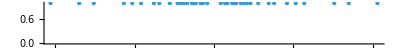

```mathematica
NumberLinePlot[symRange]
```

A transcendental range with negative step:

```mathematica
negStepRange=TranscendentalRange[100,1,-1]
```

{36 ⅇ,13 ⅇ^2,35 ⅇ,34 ⅇ,33 ⅇ,12 ⅇ^2,32 ⅇ,31 ⅇ,30 ⅇ,11 ⅇ^2,4 ⅇ^3,29 ⅇ,28 ⅇ,10 ⅇ^2,27 ⅇ,26 ⅇ,25 ⅇ,9 ⅇ^2,24 ⅇ,23 ⅇ,3 ⅇ^3,22 ⅇ,8 ⅇ^2,21 ⅇ,ⅇ^4,20 ⅇ,7 ⅇ^2,19 ⅇ,18 ⅇ,17 ⅇ,6 ⅇ^2,16 ⅇ,15 ⅇ,2 ⅇ^3,14 ⅇ,5 ⅇ^2,13 ⅇ,12 ⅇ,11 ⅇ,4 ⅇ^2,10 ⅇ,9 ⅇ,3 ⅇ^2,8 ⅇ,ⅇ^3,7 ⅇ,6 ⅇ,2 ⅇ^2,5 ⅇ,4 ⅇ,3 ⅇ,ⅇ^2,2 ⅇ,ⅇ}

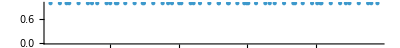

```mathematica
NumberLinePlot[negStepRange]
```

Require a lower bound on the steps:

```mathematica
boundedRange=TranscendentalRange[-2,2,1/4,1/8]
```

{-(3 ⅇ^(1/4))/2,-ⅇ^(5/4)/2,-(5 ⅇ^(1/4))/4,-ⅇ^(7/4)/4,-ⅇ^(1/4),-ⅇ^(3/2)/4,-5/(4 ⅇ^(1/4)),-7/(4 ⅇ^(3/4)),-ⅇ/4,-3/(2 ⅇ),-(√ⅇ)/4,-1/ⅇ^(5/4),-1/(4 √ⅇ),1/(4 ⅇ^2),3/(4 ⅇ^(3/2)),1/(2 √ⅇ),3/(2 ⅇ^(5/4)),2/ⅇ^(5/4),3/(2 ⅇ^(3/4)),ⅇ^(5/4)/4,ⅇ^(3/4)/2,2/(√ⅇ),ⅇ/2,2/ⅇ^(1/4),ⅇ^(5/4)/2,(3 ⅇ^(1/4))/2}

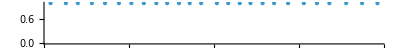

```mathematica
NumberLinePlot[boundedRange]
```

A very large transcendental range generated efficiently:

```mathematica
largeRange=TranscendentalRange[-100,100,1/2]//EchoTiming
```

2.3382

```mathematica
Length[largeRange]
```

80604

### Options

#### Method

A range in terms of logarithms:

```mathematica
logRange=TranscendentalRange[10,Method->Log]
```

{Log[3],2 Log[2],Log[5],Log[6],Log[7],3 Log[2],2 Log[3],Log[10],4 Log[2],2 Log[5],3 Log[3],5 Log[2],2 Log[6],2 Log[7],6 Log[2],4 Log[3],2 Log[10],3 Log[5],7 Log[2],3 Log[6],5 Log[3],8 Log[2],3 Log[7],3 Log[8],9 Log[2],4 Log[5],6 Log[3],3 Log[10],10 Log[2],4 Log[6],7 Log[3],4 Log[7],5 Log[5],6 Log[4],8 Log[3],5 Log[6],4 Log[10],6 Log[5],7 Log[4],5 Log[7],9 Log[3]}

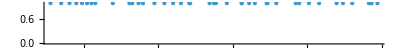

```mathematica
NumberLinePlot[logRange]
```

Ranges in terms of hyperbolic transcendental functions:

```mathematica
TranscendentalRange[-10,10,Method->Sinh]
```

{-8 Sinh[1],-7 Sinh[1],-2 Sinh[2],-6 Sinh[1],-5 Sinh[1],-4 Sinh[1],-Sinh[2],-3 Sinh[1],-2 Sinh[1],-Sinh[1],Sinh[1],2 Sinh[1],3 Sinh[1],Sinh[2],4 Sinh[1],5 Sinh[1],6 Sinh[1],2 Sinh[2],7 Sinh[1],8 Sinh[1]}

```mathematica
TranscendentalRange[3,7,Method->Tanh]
```

{4 Tanh[3],4 Tanh[4],4 Tanh[5],4 Tanh[6],4 Tanh[7],5 Tanh[3],5 Tanh[4],5 Tanh[5],5 Tanh[6],5 Tanh[7],6 Tanh[3],6 Tanh[4],6 Tanh[5],6 Tanh[6],6 Tanh[7],7 Tanh[3],7 Tanh[4],7 Tanh[5],7 Tanh[6],7 Tanh[7]}

Ranges in terms of inverse hyperbolic functions:

```mathematica
TranscendentalRange[-2,2,Method->ArcSinh]
```

{-2 ArcSinh[1],-ArcSinh[2],-ArcSinh[1],ArcSinh[1],ArcSinh[2],2 ArcSinh[1]}

```mathematica
TranscendentalRange[-2,2,1/2,Method->ArcTanh]
```

{-2 ArcTanh[1/2],-3/2 ArcTanh[1/2],-ArcTanh[1/2],-1/2 ArcTanh[1/2],1/2 ArcTanh[1/2],ArcTanh[1/2],3/2 ArcTanh[1/2],2 ArcTanh[1/2]}

Ranges in terms of trigonometric functions:

```mathematica
TranscendentalRange[-2,2,Method->Sin]
```

{-2 Sin[2],-2 Sin[1],-Sin[2],-Sin[1],Sin[1],Sin[2],2 Sin[1],2 Sin[2]}

```mathematica
TranscendentalRange[-2,2,Method->Csc]
```

{-Csc[1],-Csc[2],Csc[2],Csc[1]}

Ranges in terms of inverse trigonometric functions:

```mathematica
TranscendentalRange[-2,2,Method->ArcTan]
```

{-π/2,-ArcTan[2],-π/4,π/4,ArcTan[2],π/2}

```mathematica
TranscendentalRange[-2,2,Method->ArcCsc]
```

{-π/2,-π/3,-π/6,π/6,π/3,π/2}

Ranges in terms of Power (this requires the setting "GeneratorsDomain"->Algebraics to get non-trivial results):

```mathematica
TranscendentalRange[-3,3,Method->Power,"GeneratorsDomain"->Algebraics]
```

{3^(-2 √2),2^(-3 √2),3^(-√7),7^(-√2),2^(-(3 √7)/2),3^(-√6),7^(-(√7)/2),(2 √2)^(-√6),6^(-√2),3^(-√5),7^(-√(3/2)),6^(-(√7)/2),2^(-(3 √5)/2),5^(-√2),6^(-√(3/2)),7^(-(√5)/2),5^(-(√7)/2),6^(-(√5)/2),5^(-√(3/2)),2^(-2 √2),3^(-√3),2^(-√7),2^(-(3 √3)/2),5^(-(√5)/2),2^(-√6),7^(-(√3)/2),3^(-√2),6^(-(√3)/2),2^(-√5),(2 √2)^(-√2),3^(-(√7)/2),5^(-(√3)/2),7^(-1/(√2)),3^(-√(3/2)),6^(-1/(√2)),3^(-(√5)/2),2^(-√3),5^(-1/(√2)),2^(-√2),3^(-(√3)/2),2^(-(√7)/2),2^(-√(3/2)),3^(-1/(√2)),2^(-(√5)/2),2^(-(√3)/2),2^(-1/(√2)),2^(1/(√2)),2^((√3)/2),2^((√5)/2),3^(1/(√2)),2^(√(3/2)),2^((√7)/2),3^((√3)/2),2^(√2)}

A range in terms of a list of different types:

```mathematica
TranscendentalRange[-3,3,Method->{ArcTan,ArcSinh}]
```

{-2 ArcSinh[2],-3 ArcSinh[1],-2 ArcTan[3],-(3 π)/4,-2 ArcTan[2],-ArcSinh[3],-2 ArcSinh[1],-π/2,-ArcSinh[2],-ArcTan[3],-ArcTan[2],-ArcSinh[1],-π/4,π/4,ArcSinh[1],ArcTan[2],ArcTan[3],ArcSinh[2],π/2,2 ArcSinh[1],ArcSinh[3],2 ArcTan[2],(3 π)/4,2 ArcTan[3],3 ArcSinh[1],2 ArcSinh[2]}

A range in terms of all previous types combined:

```mathematica
completeRange=TranscendentalRange[3,Method->All]
```

{Coth[3],3 ArcCsc[3],Coth[2],3 ArcCoth[3],π/3,2 Cos[1],Log[3],Csc[2],ArcTan[2],Sinh[1],Csc[1],ArcSec[3],ArcTan[3],2 Cot[1],2 Sech[1],Coth[1],ArcCosh[2],2 Log[2],3 ArcCot[2],ArcSinh[2],2 Tanh[1],Cosh[1],Tan[1],π/2,3 Cos[1],3 ArcCoth[2],2 Sin[1],2 Csch[1],2 ArcSinh[1],ArcSinh[3],2 Sin[2],Sec[1],3 Cot[1],2 Tanh[2],3 Sech[1],2 Tanh[3],2 Coth[3],2 Coth[2],3 Log[2],(2 π)/3,2 Log[3],2 Csc[2],2 ArcTan[2],3 Tanh[1],2 Sinh[1],(3 π)/4,2 Csc[1],2 ArcSec[3],2 ArcTan[3],3 Sin[1],3 Csch[1],2 Coth[1],2 ArcCosh[2],3 ArcSinh[1],ⅇ,3 Sin[2],2 ArcSinh[2],3 Tanh[2],3 Tanh[3]}

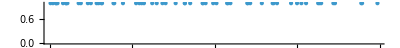

```mathematica
NumberLinePlot[completeRange]
```

#### GeneratorsDomain

A transcendental range generated by non rationals Algebraics:

```mathematica
algRange=TranscendentalRange[8,"GeneratorsDomain"->Algebraics]
```

{ⅇ,√2 ⅇ,ⅇ^(√2),√3 ⅇ,2 ⅇ,ⅇ^(√3),√2 ⅇ^(√2),√5 ⅇ,√6 ⅇ,√3 ⅇ^(√2),√7 ⅇ,ⅇ^2,2 √2 ⅇ,√2 ⅇ^(√3)}

Compare with the corresponding default range in terms of the default Rationals:

```mathematica
ratRange=TranscendentalRange[8,"GeneratorsDomain"->Rationals]
```

{ⅇ,2 ⅇ,ⅇ^2}

```mathematica
SubsetQ[algRange,ratRange]
```

True

#### FareyRange

Generate steps according to the FareySequence:

```mathematica
farRange=TranscendentalRange[1,10,1/3,"FareyRange"->True]
```

{ⅇ,(4 ⅇ)/3,ⅇ^(4/3),(3 ⅇ)/2,ⅇ^(3/2),(5 ⅇ)/3,(4 ⅇ^(4/3))/3,ⅇ^(5/3),2 ⅇ,(3 ⅇ^(4/3))/2,(4 ⅇ^(3/2))/3,(5 ⅇ^(4/3))/3,(7 ⅇ)/3,(3 ⅇ^(3/2))/2,(5 ⅇ)/2,(4 ⅇ^(5/3))/3,(8 ⅇ)/3,ⅇ^2,(5 ⅇ^(3/2))/3,2 ⅇ^(4/3),(3 ⅇ^(5/3))/2,3 ⅇ,(5 ⅇ^(5/3))/3,(7 ⅇ^(4/3))/3,2 ⅇ^(3/2),(10 ⅇ)/3,(5 ⅇ^(4/3))/2,(7 ⅇ)/2,(4 ⅇ^2)/3,(11 ⅇ)/3}

Compare with the default transcendental range of step 1/2:

```mathematica
range1over2=TranscendentalRange[1,10,1/2,"FareyRange"->False]
```

{ⅇ,(3 ⅇ)/2,ⅇ^(3/2),2 ⅇ,(3 ⅇ^(3/2))/2,(5 ⅇ)/2,ⅇ^2,3 ⅇ,2 ⅇ^(3/2),(7 ⅇ)/2}

Also the default transcendental range of step 1/3:

```mathematica
range1over3=TranscendentalRange[1,10,1/3,"FareyRange"->False]
```

{ⅇ,(4 ⅇ)/3,ⅇ^(4/3),(5 ⅇ)/3,(4 ⅇ^(4/3))/3,ⅇ^(5/3),2 ⅇ,(5 ⅇ^(4/3))/3,(7 ⅇ)/3,(4 ⅇ^(5/3))/3,(8 ⅇ)/3,ⅇ^2,2 ⅇ^(4/3),3 ⅇ,(5 ⅇ^(5/3))/3,(7 ⅇ^(4/3))/3,(10 ⅇ)/3,(4 ⅇ^2)/3,(11 ⅇ)/3}

It turns out that the transcendental Farey range does not correspond to simply combining ordinary ranges with more steps, but to a superset of it:

```mathematica
range1over2over3=SortBy[DeleteDuplicatesBy[Join[range1over2,range1over3],N],N]
```

{ⅇ,(4 ⅇ)/3,ⅇ^(4/3),(3 ⅇ)/2,ⅇ^(3/2),(5 ⅇ)/3,(4 ⅇ^(4/3))/3,ⅇ^(5/3),2 ⅇ,(5 ⅇ^(4/3))/3,(7 ⅇ)/3,(3 ⅇ^(3/2))/2,(5 ⅇ)/2,(4 ⅇ^(5/3))/3,(8 ⅇ)/3,ⅇ^2,2 ⅇ^(4/3),3 ⅇ,(5 ⅇ^(5/3))/3,(7 ⅇ^(4/3))/3,2 ⅇ^(3/2),(10 ⅇ)/3,(7 ⅇ)/2,(4 ⅇ^2)/3,(11 ⅇ)/3}

```mathematica
SubsetQ[farRange,range1over2over3]
```

True

Create a transcendental Farey range including root arguments:

```mathematica
algFareyRange=TranscendentalRange[0,3/2,1/3,"FareyRange"->True,"GeneratorsDomain"->Algebraics]
```

{ⅇ^(1/3)/3,ⅇ^((√2)/3)/3,(√ⅇ)/3,ⅇ^(2/3)/3,1/3 √2 ⅇ^(1/3),ⅇ^(1/(√2))/3,ⅇ^(1/3)/2,1/3 √2 ⅇ^((√2)/3),(√(2 ⅇ))/3,ⅇ^((√2)/3)/2,(√ⅇ)/2,1/3 ⅇ^((2 √2)/3),ⅇ/3,1/3 √2 ⅇ^(2/3),(2 ⅇ^(1/3))/3,1/3 √2 ⅇ^(1/(√2)),ⅇ^(2/3)/2,ⅇ^(1/3)/(√2),ⅇ^(1/(√2))/2,(2 ⅇ^((√2)/3))/3,(2 √ⅇ)/3,ⅇ^((√2)/3)/(√2),√(ⅇ/2),1/3 √2 ⅇ^((2 √2)/3),ⅇ^(4/3)/3,(√2 ⅇ)/3,1/2 ⅇ^((2 √2)/3),(2 ⅇ^(2/3))/3,2/3 √2 ⅇ^(1/3),(2 ⅇ^(1/(√2)))/3,ⅇ/2,ⅇ^(√2)/3,ⅇ^(2/3)/(√2),ⅇ^(1/3),ⅇ^(1/(√2))/(√2),ⅇ^(3/2)/3}

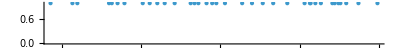

```mathematica
NumberLinePlot[algFareyRange]
```

#### FormulaComplexity

Reduce the output range by setting a threshold on the complexity:

```mathematica
TranscendentalRange[0,8,1/2,"GeneratorsDomain"->Algebraics,"FormulaComplexity"->5]
```

{ⅇ/2,√ⅇ,ⅇ/(√2),ⅇ^(1/(√2)),ⅇ,2 √ⅇ,ⅇ^2/2,√2 ⅇ,(3 ⅇ)/2,ⅇ^(√2),ⅇ^(3/2),3 √ⅇ,2 ⅇ,4 √ⅇ,(5 ⅇ)/2,ⅇ^2}

Compare with the default range with no complexity threshold:

```mathematica
TranscendentalRange[0,8,1/2,"GeneratorsDomain"->Algebraics,"FormulaComplexity"->Infinity]//Length
```

382

Compare with the same range restricted by the fourth argument (lower bound on steps):

```mathematica
TranscendentalRange[0,8,1/2,2/3,"GeneratorsDomain"->Algebraics,"FormulaComplexity"->Infinity]
```

{(√ⅇ)/2,ⅇ^((√5)/2)/2,ⅇ^(3/2)/2,ⅇ^(√2)/(√2),(√(19 ⅇ))/2,(3 √(3 ⅇ))/2,1/2 √7 ⅇ^((√7)/2),1/2 √11 ⅇ^(√(3/2)),1/2 √5 ⅇ^(√3),ⅇ^((√21)/2)/(√2),√(5/2) ⅇ^(√(5/2))}

#### WorkingPrecision

In certain cases the generated symbolic expressions may be found to collide in terms of their N numerical values:

```mathematica
machPrecRange=TranscendentalRange[20,25,Method->Tanh]
```

{21 Tanh[20],22 Tanh[20],23 Tanh[20],24 Tanh[20],25 Tanh[20]}

```mathematica
N[machPrecRange,$MachinePrecision]
```

{21.,22.,23.,24.,25.}

To distinguish them, WorkingPrecision may be optionally set to a higher value:

```mathematica
highPrecRange=TranscendentalRange[20,25,Method->Tanh,WorkingPrecision->30]
```

{21 Tanh[20],21 Tanh[21],21 Tanh[22],21 Tanh[23],21 Tanh[24],21 Tanh[25],22 Tanh[20],22 Tanh[21],22 Tanh[22],22 Tanh[23],22 Tanh[24],22 Tanh[25],23 Tanh[20],23 Tanh[21],23 Tanh[22],23 Tanh[23],23 Tanh[24],23 Tanh[25],24 Tanh[20],24 Tanh[21],24 Tanh[22],24 Tanh[23],24 Tanh[24],24 Tanh[25],25 Tanh[20],25 Tanh[21],25 Tanh[22],25 Tanh[23],25 Tanh[24],25 Tanh[25]}

```mathematica
N[highPrecRange,30]
```

{20.9999999999999998215691212778,20.99999999999999997585200649,20.9999999999999999967319244587,20.999999999999999999557714071,20.9999999999999999999401431085,20.9999999999999999999918992506,21.9999999999999998130724127672,21.9999999999999999747021020371,21.9999999999999999965763018139,21.9999999999999999995366528363,21.9999999999999999999372927804,21.9999999999999999999915135007,22.9999999999999998045757042566,22.9999999999999999735521975842,22.9999999999999999964206791691,22.9999999999999999995155916016,22.9999999999999999999344424522,22.9999999999999999999911277507,23.999999999999999796078995746,23.9999999999999999724022931314,23.9999999999999999962650565243,23.9999999999999999994945303668,23.999999999999999999931592124,23.9999999999999999999907420007,24.9999999999999997875822872354,24.9999999999999999712523886785,24.9999999999999999961094338794,24.9999999999999999994734691321,24.9999999999999999999287417959,24.9999999999999999999903562508}

### Applications

Search and find closed forms in terms of exponentials:

```mathematica
ResourceFunction["FindClosedForm"][
1.922115514,Identity,
"SearchRange"->Function[Range[#]~Join~TranscendentalRange[#]]]
```

ⅇ/(√2)

```mathematica
N[%,10]
```

1.922115514

Find closed forms in terms of all elementary transcendental functions:

```mathematica
ResourceFunction["FindClosedForm"][
1.162002218,Identity,
"SearchRange"->Function[Range[#]~Join~TranscendentalRange[1,#,1/#,Method->All]],
"MonitorSearch"->True]
```

-1/8+2 ArcCot[4/3]

```mathematica
N[%,10]
```

1.162002218

Find closed forms in terms of common mathematical functions composed to exponentials:

```mathematica
ResourceFunction["FindClosedForm"][
9.095468039,
"SearchRange"->Function[Range[#]~Join~TranscendentalRange[#]],
"MonitorSearch"->True,
"FormulaComplexity"->50]
```

-1500+Gamma[ⅇ^2]

```mathematica
N[%,10]
```

9.095468039

Search and find closed forms in terms of common functions composed to any of the available transcendental functions:

```mathematica
ResourceFunction["FindClosedForm"][
-0.01020330726,
"SearchRange"->Function[Range[-#,#]~Join~TranscendentalRange[-#,#,Method->All]],
"MonitorSearch"->True]
```

1/4 Zeta[-ArcTan[4]]

### Properties and Relations

TranscendentalRange[x,y,z] can be simply generated through the Outer product of the function #1 Exp[#2]&, with both arguments running over Range[x,y,z], suitably restricted to the elements within the bounds x, y, not belonging to the Algebraics and sorted, as follows:

```mathematica
outerTranscRange[x_,y_,z_]/;z>0:=
SortBy[DeleteDuplicatesBy[
Select[
Outer[# Exp[#2]&,Range[x,y,z],Range[x,y,z]]//Flatten,
x<=#<=y&&!Element[#,Algebraics]&],N],N]
```

```mathematica
outerRange=outerTranscRange[-2,2,1/2]
```

{-√ⅇ,-ⅇ/2,-2/(√ⅇ),-3/(2 √ⅇ),-(√ⅇ)/2,-2/ⅇ,-1/(√ⅇ),-3/(2 ⅇ),-2/ⅇ^(3/2),-1/ⅇ,-3/(2 ⅇ^(3/2)),-1/(2 √ⅇ),-2/ⅇ^2,-1/ⅇ^(3/2),-3/(2 ⅇ^2),-1/(2 ⅇ),-1/ⅇ^2,-1/(2 ⅇ^(3/2)),-1/(2 ⅇ^2),1/(2 ⅇ^2),1/(2 ⅇ^(3/2)),1/ⅇ^2,1/(2 ⅇ),3/(2 ⅇ^2),1/ⅇ^(3/2),2/ⅇ^2,1/(2 √ⅇ),3/(2 ⅇ^(3/2)),1/ⅇ,2/ⅇ^(3/2),3/(2 ⅇ),1/(√ⅇ),2/ⅇ,(√ⅇ)/2,3/(2 √ⅇ),2/(√ⅇ),ⅇ/2,√ⅇ}

```mathematica
transcRange=TranscendentalRange[-2,2,1/2]
```

{-√ⅇ,-ⅇ/2,-2/(√ⅇ),-3/(2 √ⅇ),-(√ⅇ)/2,-2/ⅇ,-1/(√ⅇ),-3/(2 ⅇ),-2/ⅇ^(3/2),-1/ⅇ,-3/(2 ⅇ^(3/2)),-1/(2 √ⅇ),-2/ⅇ^2,-1/ⅇ^(3/2),-3/(2 ⅇ^2),-1/(2 ⅇ),-1/ⅇ^2,-1/(2 ⅇ^(3/2)),-1/(2 ⅇ^2),1/(2 ⅇ^2),1/(2 ⅇ^(3/2)),1/ⅇ^2,1/(2 ⅇ),3/(2 ⅇ^2),1/ⅇ^(3/2),2/ⅇ^2,1/(2 √ⅇ),3/(2 ⅇ^(3/2)),1/ⅇ,2/ⅇ^(3/2),3/(2 ⅇ),1/(√ⅇ),2/ⅇ,(√ⅇ)/2,3/(2 √ⅇ),2/(√ⅇ),ⅇ/2,√ⅇ}

```mathematica
outerRange==transcRange
```

True

The actual implementation of TranscendentalRange[x,y,z] is much more efficient than Outer over large exponentially increasing ranges:

```mathematica
outerRange=outerTranscRange[1,1000,1];//AbsoluteTiming
```

{11.1612,Null}

```mathematica
transcRange=TranscendentalRange[1000];//AbsoluteTiming
```

{0.047206,Null}

```mathematica
outerRange==transcRange
```

True

### Possible Issues

By definition, the arguments must be all algebraic numbers:

```mathematica
TranscendentalRange[0,E,1/3]
```

Failure[…]

Bypassed this limitation by increasing the arguments:

```mathematica
TranscendentalRange[0,Ceiling[E],1/3]
```

{ⅇ^(1/3)/3,ⅇ^(2/3)/3,ⅇ/3,(2 ⅇ^(1/3))/3,ⅇ^(4/3)/3,(2 ⅇ^(2/3))/3,ⅇ^(1/3),ⅇ^(5/3)/3,(2 ⅇ)/3,(4 ⅇ^(1/3))/3,ⅇ^(2/3),(5 ⅇ^(1/3))/3,ⅇ^2/3,(2 ⅇ^(4/3))/3,(4 ⅇ^(2/3))/3,ⅇ,2 ⅇ^(1/3)}

### Neat Examples

Generate a mixed large transcendental range with all the methods available:

```mathematica
mixedRange=TranscendentalRange[-2,2,1/3,Method->All,"FareyRange"->True,"GeneratorsDomain"->Algebraics];
```

```mathematica
Length[mixedRange]
```

8878

```mathematica
RandomSample[mixedRange,10]
```

{√3 Tanh[√3],(2 Coth[4/3])/(√3),(3 Cot[1])/2,-(2 ArcSinh[1])/(√3),-1/2 ⅇ^(-(4 √2)/3),3/2 ⅇ^(-(√3)/2),√2 Csch[(4 √2)/3],-1/2 Csc[√2],-2 ArcTan[1/3],-1/3 Sinh[(2 √2)/3]}

Pick a random element of it and verify experimentally the property of being transcendental, that is that its RootApproximant expressions do not converge at any given precision:

```mathematica
randTransc=RandomChoice[mixedRange]
```

-ArcSec[-(4 √2)/3]/(√3)

```mathematica
(*Warning: the following computation can take a few minutes!*)
```

```mathematica
Table[
{prec,Magnify[InputForm@RootApproximant@N[randTransc,prec],0.7]},{prec,PowerRange[16,512,2]}]//Grid@Prepend[#,{"Precision","RootApproximant"}]&
```

Precision | RootApproximant
16 | Root[2 - 2*#1 - 2*#1^6 - 2*#1^7 - #1^11 + #1^12 - #1^13 - 2*#1^14 + #1^16 + #1^17 & , 1, 0]
32 | Root[2 + 3*#1^2 + 3*#1^3 - 4*#1^4 - #1^5 + 6*#1^6 + 2*#1^7 - 4*#1^8 - 2*#1^9 - 6*#1^10 - 3*#1^11 - 4*#1^12 - 6*#1^13 - 2*#1^14 - 2*#1^16 + 2*#1^17 + 7*#1^18 - 3*#1^20 + 2*#1^21 + 2*#1^22 & , 1, 0]
64 | Root[9 + 9*#1^2 + 11*#1^3 - 18*#1^4 + 9*#1^5 - 2*#1^6 + 2*#1^7 + 3*#1^8 - 2*#1^9 - 6*#1^10 - 9*#1^11 + 4*#1^12 + 6*#1^13 - 19*#1^14 - 8*#1^15 + 15*#1^16 + 6*#1^17 + #1^18 - 2*#1^19 + 18*#1^20 - 2*#1^21 + #1^22 + 6*#1^23 - 11*#1^24 + 4*#1^25 - 16*#1^26 - 7*#1^27 + 4*#1^28 - #1^29 - 9*#1^30 + 17*#1^31 - 4*#1^32 + 7*#1^33 - #1^34 - 3*#1^35 - 2*#1^36 - #1^38 - 3*#1^39 - #1^40 - 6*#1^41 + #1^42 - #1^43 - 2*#1^44 - 2*#1^45 - 2*#1^46 + #1^47 + #1^48 & , 1, 0]
128 | Root[-623 + 62*#1 - 511*#1^2 - 84*#1^3 + 815*#1^4 + 1010*#1^5 + 1016*#1^6 + 2119*#1^7 + 629*#1^8 - 13*#1^9 - 534*#1^10 + 532*#1^11 + 485*#1^12 - 135*#1^13 + 582*#1^14 - 597*#1^15 + 112*#1^16 - 133*#1^17 - 441*#1^18 - 577*#1^19 - 81*#1^20 + 1666*#1^21 + 602*#1^22 - 1224*#1^23 + 1217*#1^24 - 193*#1^25 - 730*#1^26 - 334*#1^27 - 942*#1^28 - 802*#1^29 + 784*#1^30 + 296*#1^31 + 528*#1^32 + 1121*#1^33 + 260*#1^34 + 186*#1^35 + 25*#1^36 - 112*#1^37 - 51*#1^38 + 3*#1^39 & , 1, 0]
256 | Root[1198316380 + 2180314257*#1 - 525363831*#1^2 + 1779499809*#1^3 - 1664786617*#1^4 + 1491163765*#1^5 + 1519767943*#1^6 + 508449621*#1^7 - 3302495916*#1^8 + 1819657398*#1^9 + 1794126776*#1^10 + 4499583*#1^11 + 611733447*#1^12 + 7394465177*#1^13 - 2056154399*#1^14 + 146795251*#1^15 + 5939698986*#1^16 + 2437930505*#1^17 - 1576340912*#1^18 + 1150344869*#1^19 - 1051538052*#1^20 - 6845865320*#1^21 - 839827779*#1^22 - 668418517*#1^23 - 1737817594*#1^24 + 38617*#1^25 & , 2, 0]
512 | Root[261814564129 - 319658680198*#1 + 135019311960*#1^2 - 840798923263*#1^3 + 289984610740*#1^4 + 1459330927775*#1^5 + 27100772004*#1^6 - 316754383253*#1^7 + 2807525969127*#1^8 + 1751121474905*#1^9 - 570433618930*#1^10 + 969880285822*#1^11 - 770767838144*#1^12 + 386171020078*#1^13 - 1432145214060*#1^14 - 3422755539760*#1^15 + 1807190110367*#1^16 + 1858847789099*#1^17 + 987108418920*#1^18 + 1497242318920*#1^19 - 1315286140853*#1^20 - 1845842381564*#1^21 - 1196290431098*#1^22 + 442827516064*#1^23 + 2038477618035*#1^24 - 467208524631*#1^25 + 3955596566536*#1^26 + 2844623837595*#1^27 - 3272874966548*#1^28 - 373512273033*#1^29 - 218469492184*#1^30 + 53188655819*#1^31 - 556891640368*#1^32 - 632613824934*#1^33 + 1112576099510*#1^34 + 906232177784*#1^35 - 674267712808*#1^36 - 1389074810611*#1^37 - 925957481697*#1^38 - 370909873892*#1^39 + 5215*#1^40 & , 1, 0]

It is interesting to do the same computation on algebraic numbers. Install this paclet to generate more general algebraic numbers:

```mathematica
PacletInstall["DanieleGregori/GeneralizedRange"]
```

PacletObject[…]

```mathematica
Get["DanieleGregori`GeneralizedRange`"]
```

Generate a large algebraic range and pick a random algebraic number in it:

```mathematica
largeAlgebraicRange={{-Graphics-, AlgebraicRange}}[-3,3,1/2,"RootOrder"->3,Method->All];
```

```mathematica
Length[largeAlgebraicRange]
```

17943

```mathematica
randAlg=RandomChoice@largeAlgebraicRange
```

-5^(1/3)/2^(2/3)-23^(1/3)/2

We find for this a quite rapid convergence beyond 64 approximation digits:

```mathematica
Table[
{prec,Magnify[InputForm@RootApproximant@N[randAlg,prec],0.7]},{prec,PowerRange[16,512,2]}]~Prepend~{"Precision","RootApproximant"}//Grid
```

Precision | RootApproximant
16 | Root[2 - #1 - 4*#1^2 + 4*#1^3 - 2*#1^4 + 4*#1^5 + 2*#1^7 - 2*#1^9 - 6*#1^11 + #1^13 & , 1, 0]
32 | Root[1 + 6*#1 - 3*#1^2 - 2*#1^3 - #1^4 - 5*#1^5 + 3*#1^6 + 2*#1^7 - 2*#1^8 - #1^9 - #1^10 - 6*#1^11 - #1^12 - #1^13 + #1^14 - #1^15 + 2*#1^16 + 7*#1^17 - 2*#1^18 + 2*#1^19 + 4*#1^20 + #1^21 & , 1, 0]
64 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]
128 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]
256 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]
512 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]

Take also the (nested) algebraic of this range which is

Find the most complex in terms of LeafCount:

```mathematica
complexAlg=TakeLargestBy[largeAlgebraicRange,LeafCount,1]//First
```

-√((3 3^(1/3))/2^(2/3)+√(3/2) 7^(1/6))

The convergence of RootApproximant is slower but necessarily happens after about 512 approximation digits:

```mathematica
Table[
{prec,Magnify[InputForm@RootApproximant@N[complexAlg,prec],0.7]},{prec,PowerRange[16,1024,2]}]~Prepend~{"Precision","RootApproximant"}//Grid
```

Precision | RootApproximant
16 | Root[-2 - #1^2 + 4*#1^3 - 2*#1^4 - #1^5 + 3*#1^6 + 4*#1^7 + 2*#1^8 - 2*#1^9 + #1^10 + #1^11 & , 1, 0]
32 | Root[-3 - 3*#1 - 3*#1^2 - 2*#1^3 + 6*#1^4 - #1^5 + #1^6 - #1^7 + 3*#1^8 - 2*#1^9 + 5*#1^10 - 5*#1^13 - 2*#1^14 - #1^15 + 7*#1^16 - #1^17 + 2*#1^18 + 2*#1^19 & , 1, 0]
64 | Root[-6 - 2*#1 - 6*#1^2 - 4*#1^3 + 7*#1^4 + 9*#1^5 + 10*#1^6 - 3*#1^7 - 11*#1^8 + 3*#1^9 - 7*#1^10 - 2*#1^11 + #1^12 - 4*#1^13 + 3*#1^14 + 13*#1^15 + 10*#1^16 + 14*#1^17 + 12*#1^18 + 13*#1^19 + 18*#1^20 + 13*#1^21 + 12*#1^22 + 12*#1^23 + 16*#1^24 + 10*#1^25 + 5*#1^26 + 6*#1^27 + 5*#1^28 + 6*#1^29 + 3*#1^30 + 2*#1^31 + 5*#1^32 + 6*#1^33 + 4*#1^34 + #1^35 & , 1, 0]
128 | Root[15 - 43*#1 + 117*#1^2 + 206*#1^3 - 82*#1^4 + 133*#1^5 - 152*#1^6 + 137*#1^7 - 18*#1^8 - 6*#1^9 - 40*#1^10 - 107*#1^11 + 142*#1^12 + 102*#1^13 - 145*#1^14 - 124*#1^15 + 33*#1^16 - 16*#1^17 - 9*#1^18 - 38*#1^19 - 60*#1^20 - 12*#1^21 + 153*#1^22 + 24*#1^23 + 85*#1^24 + 175*#1^25 + 221*#1^26 - 92*#1^27 - 5*#1^28 + 85*#1^29 + 32*#1^30 + 17*#1^31 - 6*#1^32 - 30*#1^33 + 39*#1^34 + 96*#1^35 + 21*#1^36 - 21*#1^37 + 18*#1^38 - 82*#1^39 + 69*#1^40 - 57*#1^42 - 61*#1^43 + 24*#1^44 + 22*#1^45 + 2*#1^46 - 15*#1^47 - 2*#1^48 - 6*#1^49 + 23*#1^50 + 15*#1^51 + #1^52 & , 2, 0]
256 | Root[984713 + 295442*#1 + 2799770*#1^2 - 196593*#1^3 - 166751*#1^4 - 1007953*#1^5 + 819466*#1^6 + 27332*#1^7 + 114913*#1^8 - 1709838*#1^9 - 1326392*#1^10 - 241929*#1^11 - 2318213*#1^12 + 1686458*#1^13 + 391737*#1^14 + 817944*#1^15 + 452253*#1^16 - 756709*#1^17 + 929653*#1^18 - 1502848*#1^19 - 616246*#1^20 + 257024*#1^21 - 1728340*#1^22 + 1665343*#1^23 + 646867*#1^24 - 573154*#1^25 - 184998*#1^26 + 610346*#1^27 + 613828*#1^28 + 1312139*#1^29 - 58298*#1^30 - 50867*#1^31 + 6573*#1^32 + 435034*#1^33 - 563611*#1^34 - 82465*#1^35 + 225623*#1^36 + 551831*#1^37 - 147875*#1^38 - 186022*#1^39 + 14*#1^40 & , 1, 0]
512 | Root[236372930487 - 206991309384*#1^6 - 6446961072*#1^12 - 974177280*#1^18 + 24903936*#1^24 - 497664*#1^30 + 4096*#1^36 & , 1, 0]
1024 | Root[236372930487 - 206991309384*#1^6 - 6446961072*#1^12 - 974177280*#1^18 + 24903936*#1^24 - 497664*#1^30 + 4096*#1^36 & , 1, 0]

Note this agrees with the minimal polynomial:

```mathematica
MinimalPolynomial[√((3 3^(1/3))/2^(2/3)+√(3/2) 7^(1/6))]
```

236372930487-206991309384 #1^6-6446961072 #1^12-974177280 #1^18+24903936 #1^24-497664 #1^30+4096 #1^36&

Notice the function Element can confirm the algebraic character but not always the transcendental one:

```mathematica
Element[{randAlg,complexAlg},Algebraics]
```

True

```mathematica
Element[randTransc,Algebraics]
```

ArcSec[-(4 √2)/3]∈Algebraics

It should be emphasized though that while these are easy computational investigations within the Wolfram Language, a proper rigorous mathematical proof is necessary to establish the transcendence character of a number (that is equivalent to evaluating it at infinite precision).

## Source & Additional Information

### Contributed By

Daniele Gregori

### Keywords

transcendental

numbers

range

closed forms

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Range

Algebraics

E

Pi

### Related Resource Objects

IsTranscendentalNumber

AlgebraicRange

ComplexRange

FareyRange

DanieleGregori/GeneralizedRange

FindClosedForm

### Source/Reference Citation

Alan Baker, Transcendental Number Theory (Cambridge University Press, 1975)

### Links

https://en.wikipedia.org/wiki/Transcendental_number

Mathematical constants on Wolfram Community

### Tests

Compare with test method, which is inefficient but simpler to implement (in terms of Outer instead of monotonicOuter).

#### Tests definition

```mathematica
ClearAll[test]
Options[test]={"Time"->False,"Detail"->False,"GeneratorsDomain"->Rationals};

test[{f_,2},x_,y_,z_,opts:OptionsPattern[test]]:=
	Block[{default,testing,algGen},
		
algGen=OptionValue["GeneratorsDomain"];
       
default=TranscendentalRange[x,y,z,Method->f,"GeneratorsDomain"->algGen]~EchoTiming~"smart";

testing=TranscendentalRange[x,y,z,Method->f,"Test"->True,"GeneratorsDomain"->algGen]~EchoTiming~"test";

default==testing]

test[{f_,2},c_:20,s_:2,opts:OptionsPattern[test]]:=
	Block[{det},
		det=Table[rg->
				If[!OptionValue["Time"],
					QuietEcho@test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts],
					test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts]],
			{rg,{{0,c,1/s},{-c,0,1/s},{-c,c,1/s}}}];
If[OptionValue["Detail"],Echo[det]];
If[And@@Association[det],Success["worked", <||>],Failure["failed", <||>]]]

test[All,{f_,2},c_:20,s_:2,opts:OptionsPattern[test]]:=
	Block[{det},
		det=Table[rg->
				If[!OptionValue["Time"],
					QuietEcho@test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts],
					test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts]],
			{rg,{{0,c,1/s},{c,0,-1/s},{-c,0,1/s},{0,-c,-1/s},{-c,c,1/s},{c,-c,-1/s}}}];
If[OptionValue["Detail"],Echo[det]];
If[And@@Association[det],Success["worked", <||>],Failure["failed", <||>]]]

test[All,{f_,2},{c_:20,m_:0,s_:2},opts:OptionsPattern[test]]:=
	Block[{det},
		det=Table[rg->
				If[!OptionValue["Time"],
					If[!OptionValue["Detail"],
						QuietEcho@test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts],
						test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts]],
					test[{f,2},rg[[1]],rg[[2]],rg[[3]],opts]]//Echo,
			{rg,{{m,c,s},{c,m,-s},{-c,-m,s},{-m,-c,-s},{-c-m,c-m,s},{-c+m,c+m,s},{c-m,-c-m,-s},{c+m,-c+m,-s}}}];
If[OptionValue["Detail"],Echo[det]];
If[And@@Association[det],Success["worked", <||>],Failure["failed", <||>]]]
```

#### Exp

Test of correctness

```mathematica
With[{method=Exp},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{20,2,4}

{17,2,1/3}

{20,0,3}

{20,0,2/5}

{17,1,1}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
TranscendentalRange[1,100,1,Method->Exp,"Test"->True]//EchoTiming;
TranscendentalRange[1,100,1,Method->Exp,"Test"->False]//EchoTiming;
%==%%
```

0.12884

0.004444

True

```mathematica
TranscendentalRange[100,-100,-1,Method->Exp,"Test"->True]//EchoTiming;
TranscendentalRange[100,-100,-1,Method->Exp,"Test"->False]//QuietEcho//EchoTiming;
%==%%
```

0.987958

0.554287

True

#### Log

Test of correctness

```mathematica
With[{method=Log},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{19,3,1}

{20,0,1/2}

{20,2,1/4}

{15,0,1/2}

{19,3,2/7}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->Log,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->Log,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.17278

0.0678509

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->Log,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->Log,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.318775

0.143694

True

#### Sinh

Test of correctness

```mathematica
With[{method=Sinh},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{17,0,5/2}

{15,3,1/7}

{19,4,5/3}

{18,4,2/3}

{15,2,1/5}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->Sinh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->Sinh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.11887

0.00461484

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->Sinh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->Sinh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.538478

0.0170994

True

#### Cosh

Test of correctness

```mathematica
With[{method=Cosh},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{16,3,7}

{20,4,4/7}

{19,3,3/4}

{16,5,1/5}

{16,3,3/2}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->Cosh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->Cosh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.131173

0.00479913

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->Cosh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->Cosh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.444263

0.0153407

True

#### Tanh

Test of correctness

```mathematica
With[{method=Tanh},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{18,5,2/7}

{15,3,1}

{20,3,3/2}

{19,0,4/3}

{18,0,1}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,10,1,Method->Tanh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,10,1,Method->Tanh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.0195632

0.00235103

True

```mathematica
EchoTiming[TranscendentalRange[10,-10,-1,Method->Tanh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[10,-10,-1,Method->Tanh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.0864973

0.00806387

True

#### Coth

Test of correctness

```mathematica
With[{method=Coth},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{18,3,2/5}

{19,0,3}

{17,5,7/3}

{15,2,6/5}

{15,5,7/2}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,30,1,Method->Coth,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,30,1,Method->Coth,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.514829

0.0178096

True

```mathematica
EchoTiming[TranscendentalRange[30,-30,-1,Method->Coth,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[30,-30,-1,Method->Coth,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

2.07776

0.0700458

True

#### Sech

Test of correctness

```mathematica
With[{method=Sech},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{18,1,6/5}

{16,5,3/5}

{17,4,1}

{18,5,3}

{16,5,6/7}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->Sech,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->Sech,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.13126

0.0152429

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->Sech,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->Sech,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

5.52838

0.910327

True

#### Csch

Test of correctness

```mathematica
With[{method=Csch},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{16,2,5/3}

{20,5,7/5}

{17,4,7/2}

{17,3,1/2}

{20,5,1/5}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
(*not more efficient in the former case*)
```

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->Csch,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->Csch,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.129793

0.18077

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->Csch,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->Csch,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

5.79212

0.945444

True

#### ArcSinh

Test of correctness

```mathematica
With[{method=ArcSinh},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{15,4,4}

{19,3,6/5}

{20,0,6}

{17,2,1}

{17,5,1}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcSinh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcSinh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.302764

0.0574081

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcSinh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcSinh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

1.24938

0.230366

True

#### ArcCosh

Test of correctness

```mathematica
With[{method=ArcCosh},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{20,3,6/7}

{15,5,3/5}

{15,4,3/4}

{17,3,1/6}

{16,4,1/2}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCosh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCosh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.31326

0.0523121

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCosh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCosh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.626867

0.112608

True

#### ArcTanh

Test of correctness

```mathematica
With[{method=ArcTanh},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{17,0,6/7}

{19,4,5/2}

{16,3,5}

{19,2,5/2}

{15,0,1/5}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[0,100,1/10,Method->ArcTanh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[0,100,1/10,Method->ArcTanh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.361291

0.220055

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1/10,Method->ArcTanh,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1/10,Method->ArcTanh,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%
```

1.36017

0.833092

True

#### ArcCoth

Test of correctness

```mathematica
With[{method=ArcCoth},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{18,1,7/2}

{18,3,7/4}

{17,5,1/2}

{15,0,5/4}

{17,4,2/3}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCoth,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCoth,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.248234

0.199674

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCoth,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCoth,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

1.56287

0.890935

True

#### ArcSech

Test of correctness

```mathematica
With[{method=ArcSech},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{15,2,2/3}

{15,1,5/2}

{16,4,1}

{15,3,3}

{16,2,1}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[0,10,1/10,Method->ArcSech,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[0,10,1/10,Method->ArcSech,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.0674896

0.0160233

True

```mathematica
EchoTiming[TranscendentalRange[10,-10,-1/10,Method->ArcSech,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[10,-10,-1/10,Method->ArcSech,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.133117

0.0319466

True

#### ArcCsch

Test of correctness

```mathematica
With[{method=ArcCsch},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{17,2,6}

{20,2,3}

{16,0,1/7}

{15,2,1/2}

{19,0,7/4}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCsch,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCsch,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.618411

0.247368

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCsch,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCsch,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

4.63095

0.919893

True

#### ArcSin

Test of correctness

```mathematica
With[{method=ArcSin},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{15,1,4}

{15,2,1}

{16,3,1}

{15,4,1/6}

{16,1,1/2}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[0,100,1/10,Method->ArcSin,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[0,100,1/10,Method->ArcSin,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

1.12818

0.244585

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1/10,Method->ArcSin,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1/10,Method->ArcSin,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%
```

4.6029

0.936647

True

#### ArcCos

Test of correctness

```mathematica
With[{method=ArcCos},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{19,2,1/2}

{20,4,4/3}

{18,0,7/6}

{18,2,2}

{20,0,1/2}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[0,10,1/10,Method->ArcCos,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[0,10,1/10,Method->ArcCos,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.0785046

0.0204606

True

```mathematica
EchoTiming[TranscendentalRange[10,-10,-1/10,Method->ArcCos,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[10,-10,-1/10,Method->ArcCos,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.267513

0.0674724

True

#### ArcTan

Test of correctness

```mathematica
With[{method=ArcTan},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{19,3,7/5}

{16,2,5/2}

{15,2,6}

{19,0,5/2}

{18,5,3/4}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcTan,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcTan,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.347201

0.165744

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcTan,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcTan,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

1.25285

0.62896

True

#### ArcCot

Test of correctness

```mathematica
With[{method=ArcCot},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{15,0,3/2}

{19,4,1/3}

{20,0,1/2}

{18,5,1/3}

{20,3,1}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCot,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCot,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.275429

0.222139

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCot,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCot,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

1.69962

0.954783

True

#### ArcSec

Test of correctness

```mathematica
With[{method=ArcSec},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{15,5,2/7}

{18,3,7/4}

{17,4,4/5}

{16,4,2/5}

{16,2,6}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcSec,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcSec,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.906539

0.19347

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcSec,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcSec,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

3.47948

0.746523

True

#### ArcCsc

Test of correctness

```mathematica
With[{method=ArcCsc},Table[With[{args = {RandomInteger[{15, 20}], RandomInteger[{0, 5}], RandomInteger[{1, 7}]/RandomInteger[{1, 7}]} // Echo},
  test[All, {method, 2}, args] // QuietEcho], 5]]
```

{15,0,1}

{20,1,2/3}

{20,0,1/5}

{16,1,3/7}

{19,3,3/2}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCsc,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,100,1,Method->ArcCsc,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

0.757255

0.241865

True

```mathematica
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCsc,"Test"->True],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[100,-100,-1,Method->ArcCsc,"Test"->False]//QuietEcho,Method->RepeatedTiming];
%==%%
```

5.50088

1.02347

True

#### Power

Test of correctness

```mathematica
With[{method=Power},Table[With[{args = {RandomInteger[{5, 8}], RandomInteger[{0, 4}], RandomInteger[{1, 5}]/RandomInteger[{1, 5}]} // Echo},
  test[All, {method, 2}, args,"GeneratorsDomain"->Algebraics] // QuietEcho], 5]]
```

{6,0,3/4}

{6,3,3}

{5,4,3/5}

{5,0,1}

{8,4,4/3}

{Success[…],Success[…],Success[…],Success[…],Success[…]}

Test of efficiency

```mathematica
EchoTiming[TranscendentalRange[1,20,1,Method->Power,"Test"->True,"GeneratorsDomain"->Algebraics],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[1,20,1,Method->Power,"Test"->False,"GeneratorsDomain"->Algebraics]//QuietEcho,Method->RepeatedTiming];
%==%%
```

6.07783

0.112288

True

```mathematica
EchoTiming[TranscendentalRange[10,-10,-1,Method->Power,"Test"->True,"GeneratorsDomain"->Algebraics],Method->RepeatedTiming];
EchoTiming[TranscendentalRange[10,-10,-1,Method->Power,"Test"->False,"GeneratorsDomain"->Algebraics]//QuietEcho,Method->RepeatedTiming];
%==%%
```

7.12879

0.615094

True

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

For all the methods implemented in TranscendentalRange[x,y,z,Method->All], the transcendental character of the generated expressions is formally established as corollary to the theorems of Lindemann-Weierstrass and Baker (cf. Alan Baker, 1975, "Transcendental Number Theory", Cambridge University Press).

Actually, this first version implements only a minimal subset of all possible expressions which these theorems prove to be transcendental numbers. I hope to implement also more general possibilities and a more efficient algorithm in later versions.

## Submission Notes

Additional information for the reviewer.